```mathematica
(* Simulation to check single traveling wave solution behavior *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=20000;
verbose=False;
veryverbose=False;
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{2,1},{3,1},{4,1},{5,1},{6,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulations to compare *)
SeedRandom[100];
fulldata=0;
results0=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
SeedRandom[100];
fulldata=1;
results1=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
```

```mathematica
(* Compare Data Collected *)
comparedata0=results0[[;;,1;;10]];
comparedata1 = getSummarizedResults[results1,Δc1,Δc2,popsize];
Total[comparedata0-comparedata1]
```

{0.,0.,0.,0.,-3.16026×10^-18,3.47982×10^-18,-2.29364×10^-17,0.,-6.43929×10^-15,0.}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Linear combination experiment w/ evolution in 2 dimensions *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.02,0.02,2 10^-4,2 10^-4,10^7};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactflag}={0,False,False,False};
```

```mathematica
(* Run simulation *)
SeedRandom[7];
simdata=ParallelTable[
(* Set initial genotypes and their abundances *)
Print["Trial ",i];
λ1=(Mod[i,21,1]-1)/20;
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2];
results=RunSimulationCheckEachMutation2[popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/v2dtest/v2dtest_N-10p7_c-0d02_U-2x10pn4_exp"<>ToString[i]<>".m",{results,popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2}];
{Mean[results[[;;,9]]],popsize,λ1 Δc1,(1-λ1)Δc2,λ1 U1,(1-λ1)U2}
,{i,1,210}];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store only summary data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^10};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={0,False,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

Trait 2 q = 8. in Concurrent Mutations Regime with expected time scale 65.7881 and rate of adaptation 0.000152003

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m",results];
```

mean substitution load = 0.077788

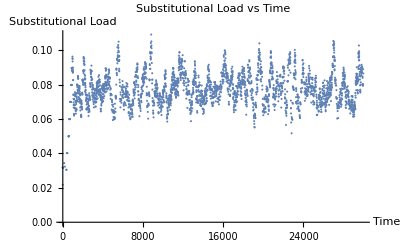

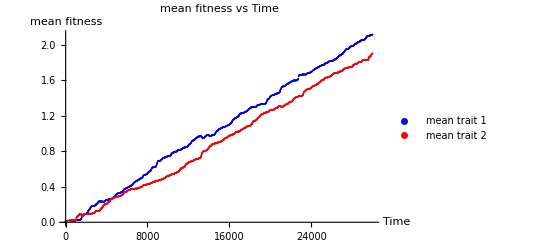

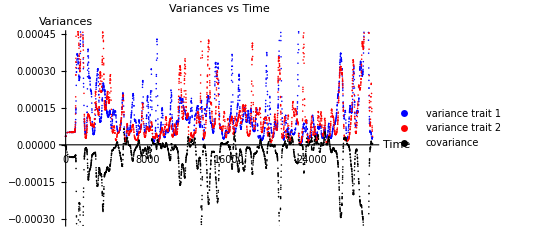

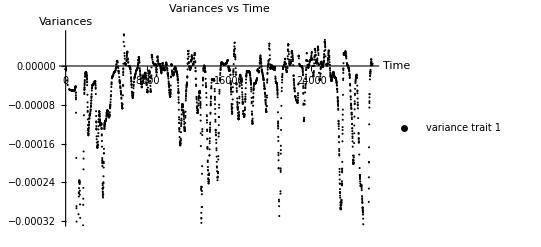

mean covariance -0.0000756336

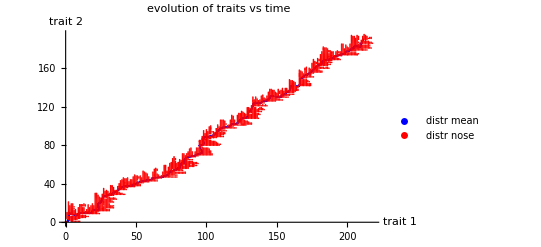

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Print["mean substitution load = ",meansubload];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{timesAndCov},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
Print["mean covariance ",Mean[timesAndCov[[;;,2]]]];
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"evolution of traits vs time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^11};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

Trait 2 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",results];
```

```mathematica
results1=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
results2=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
Mean[results1[[2;;-1,{1}]]-results1[[1;;-2,{1}]]]
StandardDeviation[results1[[2;;-1,{1}]]-results1[[1;;-2,{1}]]]
Mean[results2[[2;;-1,{1}]]-results2[[1;;-2,{1}]]]
StandardDeviation[results2[[2;;-1,{1}]]-results2[[1;;-2,{1}]]]
meanPDF1=getMeanPDF[results1[[1;;-1]]];
meanPDF2=getMeanPDF[results2[[1;;-1]]];
```

{6.65188}

{7.71933}

{10.5263}

{10.6698}

```mathematica
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",meanPDF1];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",meanPDF2];
```

```mathematica
meanPDF1[[2]]=(1/Total[meanPDF1[[2]]])meanPDF1[[2]];
meanPDF2[[2]]=(1/Total[meanPDF2[[2]]])meanPDF2[[2]];
pdfsurf1=Table[{meanPDF1[[1]][[i]][[1]],meanPDF1[[1]][[i]][[2]],Log[meanPDF1[[2]][[i]]]},{i,1,Length[meanPDF1[[1]]]}];
pdfsurf2=Table[{meanPDF2[[1]][[i]][[1]],meanPDF2[[1]][[i]][[2]],Log[meanPDF2[[2]][[i]]]},{i,1,Length[meanPDF2[[1]]]}];
```

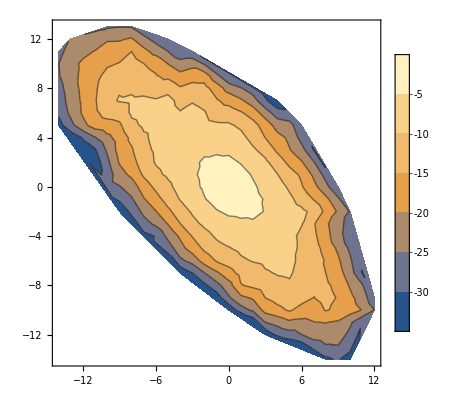

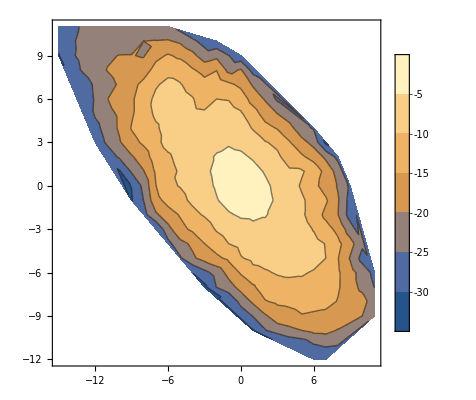

```mathematica
ListContourPlot[pdfsurf1,PlotRange->All,PlotLegends->Automatic]
ListContourPlot[pdfsurf2,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^11};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

Trait 2 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m",results];
```

```mathematica
getMeanPDF[results_]:=Module[{truepopsize,trait1mean,trait2mean,meanPDF,matchflag},
(* initialize local variables *)
meanPDF={{},{}};
matchflag=False;

Do[ (* Loop through all possible results *)
truepopsize = Total[results[[i]][[3]]];
trait1mean=Round[results[[i]][[4]][[1]]];
trait2mean=Round[results[[i]][[4]][[2]]];

Do[ (* For each result run through current list in meanPDF, check if fit.class present, then add abundance or update *)
Do[ (* Run through list of current meanPDF *)
If[Length[meanPDF[[1]]]==0,
meanPDF[[1]]=Join[meanPDF[[1]],{results[[i]][[2]][[k]]-{trait1mean,trait2mean}}];
meanPDF[[2]]=Join[meanPDF[[2]],{(1/truepopsize)results[[i]][[3]][[k]]}];,
If[meanPDF[[1]][[l]]==(results[[i]][[2]][[k]]-{trait1mean,trait2mean}),
meanPDF[[2]][[l]]+=(1/truepopsize)results[[i]][[3]][[k]]; matchflag=True;];];
,{l,1,Max[1,Length[meanPDF[[1]]]]}];
If[!matchflag,
meanPDF[[1]]=Join[meanPDF[[1]],{results[[i]][[2]][[k]]-{trait1mean,trait2mean}}];
meanPDF[[2]]=Join[meanPDF[[2]],{(1/truepopsize)results[[i]][[3]][[k]]}];,matchflag=False];
,{k,1,Length[results[[i]][[2]]]}];
,{i,1,Length[results]}];
meanPDF
]
```

```mathematica
results1=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
results2=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m"];
meanPDF1=getMeanPDF[results1];
meanPDF2=getMeanPDF[results2];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",meanPDF1];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m",meanPDF2];
```

```mathematica
meanPDF1[[2]]=(1/Total[meanPDF1[[2]]])meanPDF1[[2]];
meanPDF2[[2]]=(1/Total[meanPDF2[[2]]])meanPDF2[[2]];
```

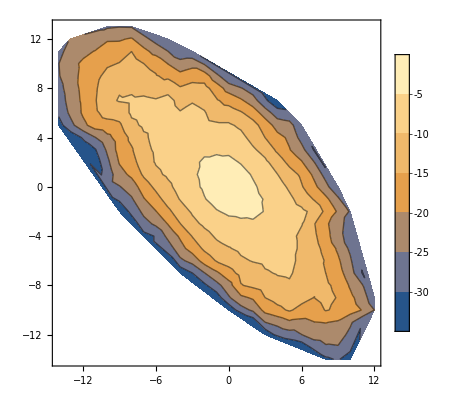

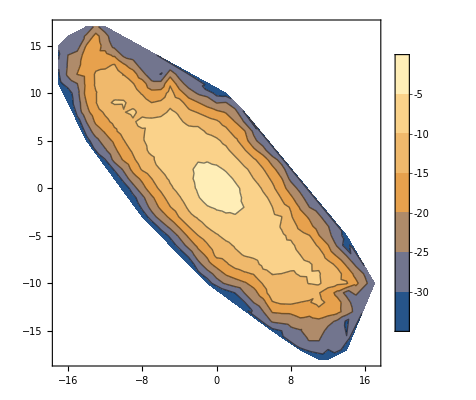

```mathematica
pdfsurf1=Table[{meanPDF1[[1]][[i]][[1]],meanPDF1[[1]][[i]][[2]],Log[meanPDF1[[2]][[i]]]},{i,1,Length[meanPDF1[[1]]]}];
pdfsurf2=Table[{meanPDF2[[1]][[i]][[1]],meanPDF2[[1]][[i]][[2]],Log[meanPDF2[[2]][[i]]]},{i,1,Length[meanPDF2[[1]]]}];
ListContourPlot[pdfsurf1,PlotLegends->Automatic]
ListContourPlot[pdfsurf2,PlotLegends->Automatic]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-5,1 10^-5,10^11};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 6.83154 in Concurrent Mutations Regime with expected time scale 118.455 and rate of adaptation 0.0000844201

Trait 2 q = 6.83154 in Concurrent Mutations Regime with expected time scale 118.455 and rate of adaptation 0.0000844201

```mathematica
(* Run simulation *)
SeedRandom[16];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn5_U2-1x10pn5_exp005.m",results];
```

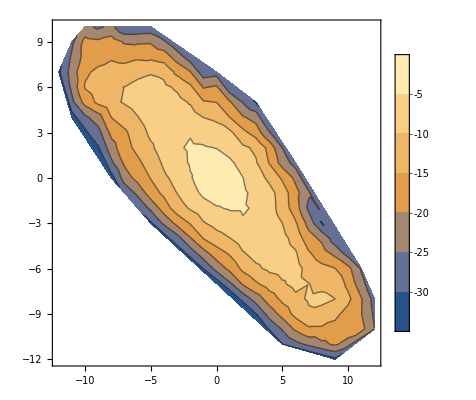

```mathematica
meanPDF3=getMeanPDF[results];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn5_U2-1x10pn5_exp003.m",meanPDF3];
meanPDF3[[2]]=(1/Total[meanPDF3[[2]]])meanPDF3[[2]];
pdfsurf3=Table[{meanPDF3[[1]][[i]][[1]],meanPDF3[[1]][[i]][[2]],Log[meanPDF3[[2]][[i]]]},{i,1,Length[meanPDF3[[1]]]}];
ListContourPlot[pdfsurf3,PlotLegends->Automatic]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-7,1 10^-7,10^11};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 4.02824 in Concurrent Mutations Regime with expected time scale 380.185 and rate of adaptation 0.000026303

Trait 2 q = 4.02824 in Concurrent Mutations Regime with expected time scale 380.185 and rate of adaptation 0.000026303

```mathematica
(* Run simulation *)
SeedRandom[32];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn7_U2-1x10pn7_exp006.m",results];
```

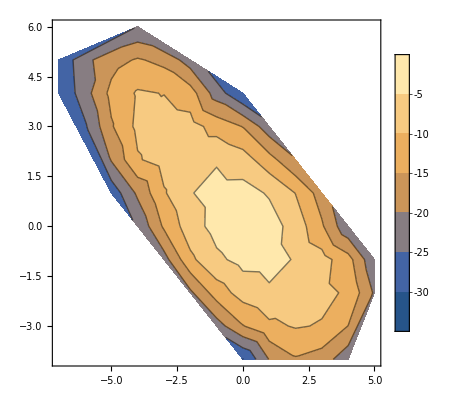

```mathematica
meanPDF3=getMeanPDF[results];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn7_U2-1x10pn7_exp006.m",meanPDF3];
meanPDF3[[2]]=(1/Total[meanPDF3[[2]]])meanPDF3[[2]];
pdfsurf3=Table[{meanPDF3[[1]][[i]][[1]],meanPDF3[[1]][[i]][[2]],Log[meanPDF3[[2]][[i]]]},{i,1,Length[meanPDF3[[1]]]}];
ListContourPlot[pdfsurf3,PlotLegends->Automatic]
```